```mathematica
(* Created april 14th during an earthquake *)

ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]


pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 2 Kb

{Utilities`CleanSlate`,DocumentationSearch`,ResourceLocator`,WolframAlphaClient`,CloudPublishMenu`,ExternalEvaluateLoader`,SystemTools`,PacletManager`,System`,Global`}

```mathematica
Hyperlink["Book",
"https://www.cambridge.org/core/books/hydrodynamic-stability/A0E78BC88D5572AED79CCCE8B977707C"]
```

[Book](https://www.cambridge.org/core/books/hydrodynamic-stability/A0E78BC88D5572AED79CCCE8B977707C)

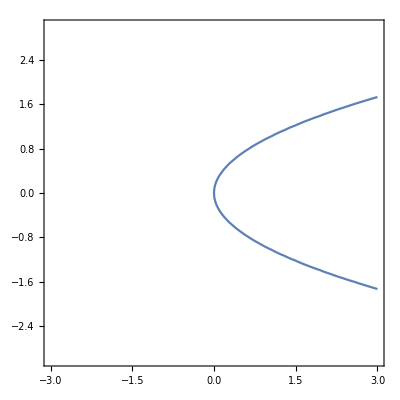

```mathematica
ContourPlot[y^2==x , {x,-3,3},{y,-3,3}]
```

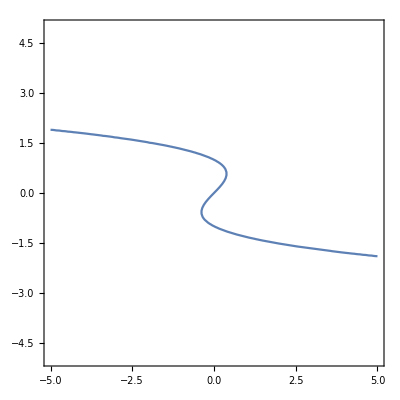

```mathematica
ContourPlot[ R == U-U^3, {R,-5,5},{U,-5,5}]
```

```mathematica
(* Page 24 *)
```

```mathematica
Clear[example2pt9]
example2pt9  = 
{
x'[t] == - y + ( a - x^2-y^2) x ,
y'[t] == x + ( a-x^2-y^2) y 
} ;
example2pt9 // MatrixForm // TraditionalForm
```

(x'(t)==x (a-x^2-y^2)-y
y'(t)==y (a-x^2-y^2)+x)

```mathematica
(* Rewrite a module to look at 
RHS of ODE's and just pick out coefficients of x and y
```

```mathematica
Coefficient[example2pt9[[1,2]],y]
```

-1

```mathematica
Coefficient[example2pt9[[1,2]],x]
```

a-y^2

```mathematica
CoefficientList[example2pt9[[1,2]],{x,y}]
```

{{0,-1,0},{a,0,-1},{0,0,0},{-1,0,0}}

```mathematica
CoefficientList[1+a x^2+b x y+c y^2+d x + f y ,{x,y}] // MatrixForm
```

(1 | f | c
d | b | 0
a | 0 | 0)

```mathematica
Coefficient[1+a x^2+b x y+c y^2+d x + f y, x]
```

d+b y